```mathematica
LECs=SemanticImport["/home/johannesk/kette_repo/source/AcoreNteraction/data/LECs.dat"];
```

C_0 = -183.481 MeV      Λ = 1.62563 fm^-2

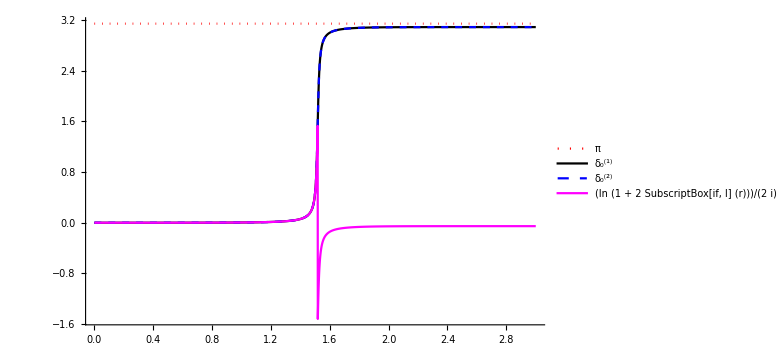
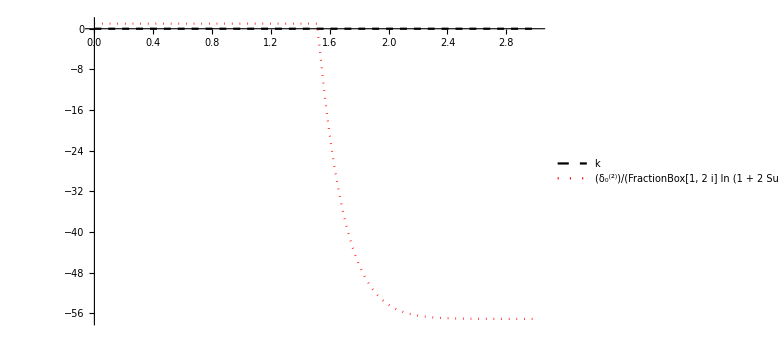
-Graphics- | -Graphics-

```mathematica
lamnumber=50;
ClearAll;
Poti[r_,a_,b_]:=a  Exp[-b r^2];
mm=938;
lam=LECs[[lamnumber]][[1]];
lec=LECs[[lamnumber]][[2]];
Print["C_0 = "<>ToString[lec]<>   " MeV      Λ = "<>ToString[lam^2/4]<>" fm^-2"];
hbarc=197.0;
l=0;
k=0.001;
r0=0.00001;rMax=3;

delta0=NDSolve[{d0'[r]==-1./k (mm/hbarc^2 Poti[r,lec,lam^2/4]) Sin[k r+d0[r]]^2,d0[r0]==0.0},d0,{r,r0,rMax}];
deltal=NDSolve[{dl'[x]==-k^(-1) mm/hbarc^2 Poti[x,lec,lam^2/4]((k x) SphericalBesselJ[l,k x] Cos[dl[x]]-(k x) SphericalBesselY[l,k x] Sin[dl[x]])^2 ,dl[r0]==0.0},dl,{x,r0,rMax}];
ampll=NDSolve[{fl'[x]==-k^(-1) mm/hbarc^2 Poti[x,lec,lam^2/4]((k x) SphericalBesselJ[l,k x]+I (k x) (SphericalBesselJ[l,k x] +I SphericalBesselY[l,k x]) fl[x])^2 ,fl[r0]==0.0},fl,{x,r0,rMax}];

Grid[{{
Plot[{Pi,Evaluate[dl[r]/.deltal],Evaluate[d0[r]/.delta0],Re[Log[1+2 I Evaluate[fl[r]/.ampll]]/(2 I)]},{r,r0,rMax},ImageSize->Large,PlotStyle->{{Red,Dotted},{Opacity->0.2,Black},{Dashed,Blue},{Magenta}},PlotRange->All,PlotLegends->{"π","δ_0^(1)","δ_0^(2)","(ln (1 + 2 SubscriptBox[if, l] (r)))/(2  i)"}],
Plot[{k,Evaluate[d0[r]/.delta0]/Re[Log[1+2 I Evaluate[fl[r]/.ampll]]/(2 I)]},{r,r0,rMax},ImageSize->Large,PlotStyle->{{Black,Dashed},{Red,Dotted}},PlotRange->Full,PlotLegends->{"k","δ_0^(2)/(FractionBox[1, 2  i] ln (1 + 2 SubscriptBox[if, l] (r)))"}]
}}]
```

purely imaginary momentum κ

```mathematica
ampll[κ_]:=NDSolve[{gl'[x]==-2/κ (mm/hbarc^2 Poti[x,lec,lam^2/4]) (I κ x)(I^(l+1) (SphericalBesselJ[l,I κ x] +I SphericalBesselY[l,I κ x]) Sin[gl[r]]+I^(-l-1) SphericalBesselJ[l,I κ x] Cos[gl[r]]),fl[r0]==0.0},fl,{x,r0,rMax}];

Plot[{Pi,Evaluate[dl[r]/.deltal],Evaluate[d0[r]/.delta0],Re[Log[1+2 I Evaluate[fl[r]/.ampll]]/(2 I)]},{r,r0,rMax},ImageSize->Large,PlotStyle->{{Red,Dotted},{Opacity->0.2,Black},{Dashed,Blue},{Magenta}},PlotRange->All,PlotLegends->{"π","δ_0^(1)","δ_0^(2)","(ln (1 + 2 SubscriptBox[if, l] (r)))/(2  i)"}]
```